# Bifurcations

## Set up our graphics tooling.

```mathematica
bifurcationPlot=f↦Module[
{
sign=D[f,x]>0
},
Show[
ContourPlot[If[sign,1,Null]f==0,{r,-3,3},{x,-3,3},ContourStyle->Dashed,FrameLabel->{"r","x^*"}],
ContourPlot[If[sign,Null,1]f==0,{r,-3,3},{x,-3,3}]
]
];
phasePlot=f↦Manipulate[
Module[{
sign=D[f,x]>0,
nodes=Select[#∈Reals&]@
(x/.Solve[f==0,x])
},
Plot[f,{x,-3,3},PlotRange->{-5,5},
Epilog->{
PointSize[Large],
Point[Map[{#,0}&]@Select[Not[sign/.(x->#)]&]@nodes],
Point[Map[{#,0}&]@Select[sign/.(x->#)&]@nodes],
White,
Point[Map[{#,0}&]@Select[sign/.(x->#)&]@nodes]
},AxesLabel->{"x", "dx/dt"}]
],
{r,-3,3}
];
```

## Saddle Node Bifurcation

r+x^2

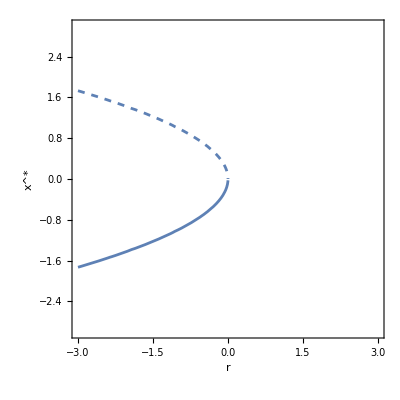

```mathematica
r +x^2
phasePlot[%]
bifurcationPlot[%%]
```

## Transcritical Bifurcation

r x-x^2

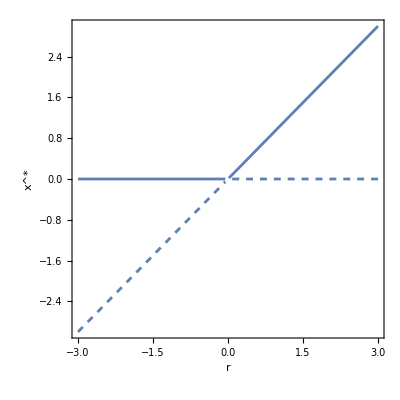

```mathematica
r x -x^2
phasePlot[%]
bifurcationPlot[%%]
```

## Pitchfork Bifurcation

### Supercritical

r x-x^3

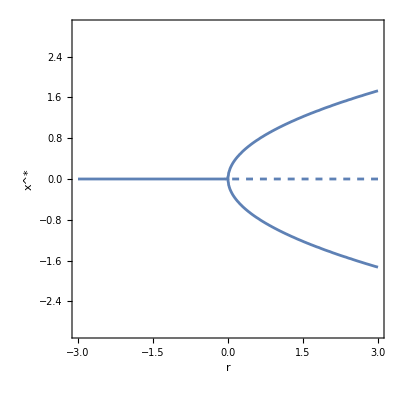

```mathematica
r x -x^3
phasePlot[%]
bifurcationPlot[%%]
```

### Subcritical

r x+x^3-x^5

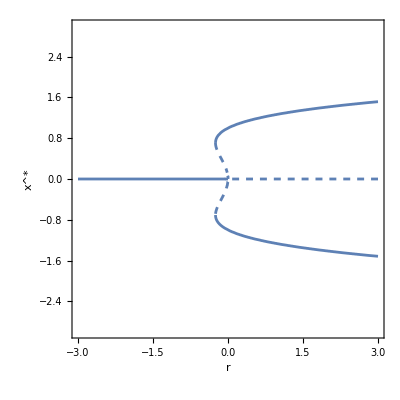

```mathematica
r x +x^3-x^5
phasePlot[%]
bifurcationPlot[%%]
```

### Imperfect and Catastrophe

```mathematica
-r x -x^3+h
Manipulate[
bifurcationPlot[%],
{{h,0},-3,3}
]
```

h-r x-x^3

### Insect Outbreak

```mathematica
bifurcationPlot2=f↦Module[
{
sign=D[f,x]>0
},
Show[
ContourPlot[If[sign,1,Null]f==0,{r,0,1},{x,0,15},ContourStyle->Dashed,FrameLabel->{"r","x^*"}],
ContourPlot[If[sign,Null,1]f==0,{r,0,1},{x,0,15}]
]
];
bifurcationPlot3=f↦Module[
{
sign=D[f,x]>0
},
Show[
ContourPlot[If[sign,1,Null]f==0,{k,0,15},{x,0,15},ContourStyle->Dashed,FrameLabel->{"k","x^*"}],
ContourPlot[If[sign,Null,1]f==0,{k,0,15},{x,0,15}]
]
];
```

```mathematica
Manipulate[
bifurcationPlot2[r x(1-x/k)-x^2/(1+x^2)],
{{k,10},0,15}
]
Manipulate[
bifurcationPlot3[r x(1-x/k)-x^2/(1+x^2)],
{{r,0.54},0,1}
]
```

## Reference

Strogatz, Steven H. Nonlinear Dynamics and Chaos : With Applications to Physics, Biology, Chemistry, and Engineering. Second edition. Boca Raton, FL ; CRC Press, Taylor & Francis Group, 2018. Print.
Chapter 3